```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
```

## Line Types

```mathematica
actin[l_]:=Graphics[
{Red,
Arrowheads[0.004],
Arrow[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];
amotor[l_]:=Graphics[
{Green,
Thick,
Arrowheads[{-0.005,0.005}],
Arrow[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];
pmotor[l_]:=Graphics[
{Blue,
Thick,
Arrowheads[{-0.005,0.005}],
Arrow[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
nparticles=Differences[Position[particles,"t",2]][[1,1]]-1;
dt=particles[[2+nparticles,3]];
particlesT=Partition[particles[[2;;]],nparticles, nparticles+1];
{nparticles, dt,particlesT}
];
```

## Simulator

```mathematica
sim[d_,deltat_,genMovie_]:=
Module[
{dir=d,
Δt=deltat,
movieflag=genMovie},
(*Load Data*)
        {nrods,dt,rt}=ParticleTimeSeries[dir,"rods"]; 
   {npms,dt,pmt}=ParticleTimeSeries[dir,"amotors"]; 
   {nams,dt,amt}=ParticleTimeSeries[dir,"pmotors"]; 
maxFrame=Min[Length[amt],Length[pmt],Length[rt]];
Print["Generating frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
frames=Table
[
Show[
Join[
Table[
actin[rt[[t,i]]],
{i,Length[rt[[t]]]}
],
Table[
amotor[amt[[t,i]]],
{i,Length[amt[[t]]]}
],
Table[
pmotor[pmt[[t,i]]],
{i,Length[pmt[[t]]]}
]
]
,Frame->True,Background->Black,PlotRange->{{-25,25},{-25,25}},FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*(t-1)]<>" s "},BaseStyle->{FontSize->16,FontColor->White}
]
,{t,1,maxFrame,Δt}
];
If[movieflag, Export[dir<>"/data/movie.avi",frames]];
frames
];
```

```mathematica
ρs={"0",".08",".16",".24",".32",".40",".48",".56",".64",".72",".80"};
basedir="clnk_nm12_np500_tf1000_amRho.05_pmRho";
dirs=Table[basedir<>ρ,{ρ,ρs}];
```

```mathematica
lds={".249",".332",".415",".498",".581",".664",".747",".830"};
basedir="clnk_nm12_np500_pmRho.64_ld";
dirs=Table[basedir<>l,{l,lds}];
```

```mathematica
temps={".0008",".0072",".0080"};
basedir="nmon120_temp";
dirs=Table[basedir<>t,{t,temps}];
```

```mathematica
nmons=Table[ToString[i],{i,8,40,2}];
nmonsHi=Table[ToString[i],{i,45,100,5}];
basedir="fixed_total_length_nmon";
dirs=Table[basedir<>n,{n,Join[nmons,nmonsHi]}];
```

```mathematica
seeds=Table[ToString[i],{i,10}];
basedir="nmon50_seed";
dirs=Table[basedir<>s,{s,seeds}];
```

```mathematica
seedframes=Table[sim[mdwlcl<>dr,1,False],{dr,dirs}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed1/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed1/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed1/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed1

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed2/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed2/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed2/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed2

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed3/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed3/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed3/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed3

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed4/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed4/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed4/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed4

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed5/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed5/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed5/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed5

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed6/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed6/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed6/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed6

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed7/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed7/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed7/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed7

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed8/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed8/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed8/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed8

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed9/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed9/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed9/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed9

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed10/txt_stack/rods.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed10/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed10/txt_stack/pmotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed10

```mathematica
Length[seedframes]
```

2001

In the nmon50 seed experiments
Last good frame :
  1 - 512
2 - all good
3 - 510
4 - 858
5 - 663
6 - 538
7 - 463
8 - 522
9 - 733
10- 406

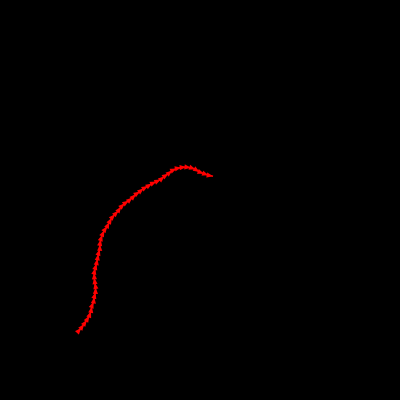
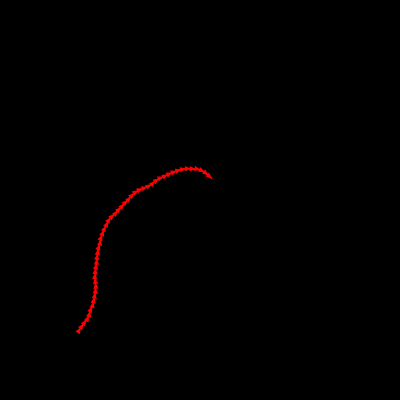
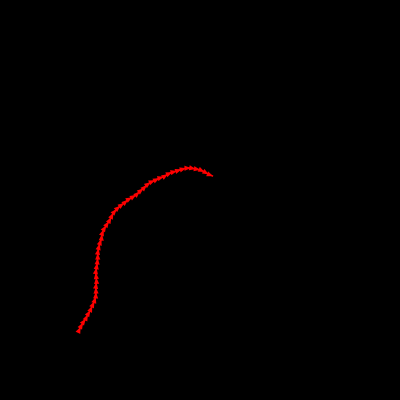
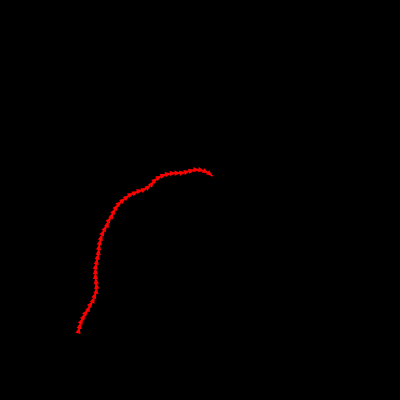
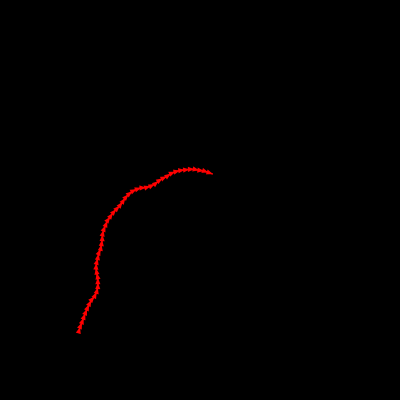
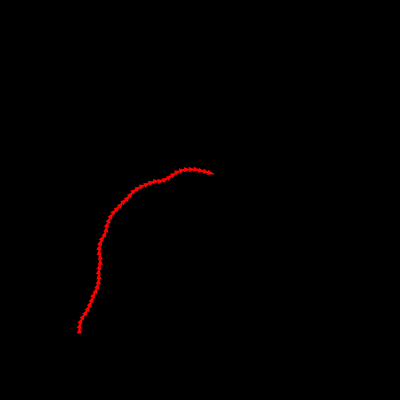
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[seedframes[[10,i]],{i,400,410}]
```

```mathematica
mdwout<>dirs[[6]]
```

/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/clnk_nm12_np500_tf1000_amRho.05_pmRho.40

Still waiting for a safe time to evaluate $Inspector[]

$Aborted

```mathematica
Length[frames]
```

```mathematica
Length[frames]
```

1

```mathematica
Length[rt]
```

3

```mathematica
rt[[1]]
```

$Failed⟦2;;All⟧

```mathematica
{nrods,dt,rt}=ParticleTimeSeries[mdwout<>dirs[[6]],"rods"];
```

$Aborted